## Some basics in Mathematica

```mathematica
x
```

x

```mathematica
α=1
```

1

```mathematica
α
```

1

```mathematica
N[π,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
σ=2;
μ=0;
Manipulate[
Plot[1/(√(2π σ^2))ⅇ^(-(x-μ)^2/(2 σ^2)),{x,-10,10},PlotRange->All],
{μ,-1,1},{σ,1,4}
]
```

```mathematica
Manipulate[
Plot3D[
Sin[f x]Cos[y^2],
{x,-2,2},{y,-2,2}],
{f,1,3}
]
```

```mathematica
Integrate[Log[x]^2 Sin[x],x]
```

ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},-ⅈ x]-ⅈ x HypergeometricPFQ[{1,1,1},{2,2,2},ⅈ x]-Log[x] (2 EulerGamma+Gamma[0,-ⅈ x]+Gamma[0,ⅈ x]+Log[-ⅈ x]+Log[ⅈ x]-Log[x]+Cos[x] Log[x])

```mathematica
NIntegrate[Log[x]^2 Sin[x],{x,0,1}]
```

0.244868

```mathematica
f[x]
```

f[x]

```mathematica
Clear[f]
```

```mathematica
DSolve[{
D[f[x,t],t,t]-D[f[x,t],x,x]==0,
f[x,0]==0
},f,{x,t}]
```

{{f→Function[{x,t},-ⅈ √(π/2) C[2] DiracDelta[-t+x]+ⅈ √(π/2) C[2] DiracDelta[t+x]]}}

```mathematica
sol=f/.NDSolve[{
D[f[x,t],t]-D[f[x,t],x]==0,
f[x,0]==Sin[2π x],
f[0,t]==f[1,t]
},f,{x,0,1},{t,0,1}]⟦1⟧
```

InterpolatingFunction[…]

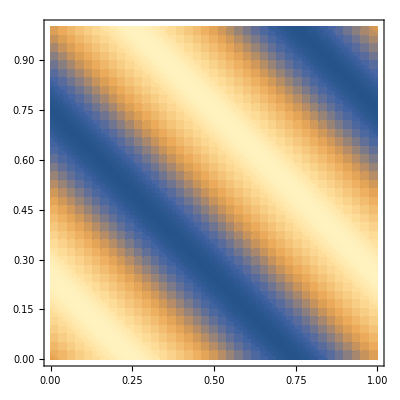

```mathematica
DensityPlot[sol[x,t],{x,0,1},{t,0,1},PlotPoints->40]
```